## p. 46

```mathematica
p=(2x+4)/(x-3)
```

(4+2 x)/(-3+x)

```mathematica
Reduce[p<0]
```

-2<x<3

```mathematica
Indeterminate
Limit[p,x->3]
```

Indeterminate

Indeterminate

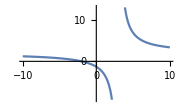

```mathematica
Plot[p,{x,-10,10},PlotTheme->"Minimal",ImageSize->Small]
```

```mathematica
d=D[p,x]
```

2/(-3+x)-(4+2 x)/(-3+x)^2

```mathematica
Simplify[d]
```

-10/(-3+x)^2

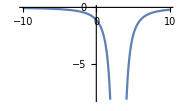

```mathematica
Plot[d,{x,-10,10},PlotTheme->"Minimal",ImageSize->Small]
```

Inversão do sinal do expoente da variável independente.

```mathematica
Plot[p,{x,-10,10},PlotTheme->"Default",ImageSize->Small]
```

-Graphics-

```mathematica
pi=p^-1
```

(-3+x)/(4+2 x)

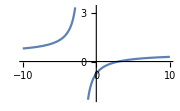

```mathematica
Plot[pi,{x,-10,10},PlotTheme->"Default",ImageSize->Small]
```

Derivadas são limites.

```mathematica
f=x^2+2
```

2+x^2

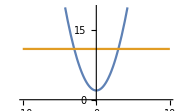

```mathematica
Plot[{f,11},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{0,20}}]
```

```mathematica
Limit[f, x -> 3]
```

11

```mathematica
48^2
363-48
315/7
243/9
147/7
```

2304

315

45

27

21

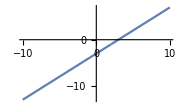

```mathematica
Clear[fp113f]
fp113f[x_]:=(x^2-5x+6)/(x-2)
Plot[fp113f[x],{x,-10,10},ImageSize->Small]
```

```mathematica
{fp113f[0],fp113f[1],fp113f[2],fp113f[3],fp113f[4]}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{-3,-2,Indeterminate,0,1}

```mathematica
PolynomialQuotientRemainder[x^2-5x+6,x-2,x] //TraditionalForm
```

{x-3,0}

```mathematica
PolynomialQuotientRemainder[x^2-9x-10,x+1,x] // TraditionalForm
```

{x-10,0}

```mathematica
PolynomialQuotientRemainder[x^3-4 x^2+2x-3,x+2,x] // TraditionalForm
```

{x^2-6 x+14,-31}

```mathematica
PolynomialQuotientRemainder[x^3-4 x^2+2x-3,x+2,x] // TraditionalForm
```

{x^2-6 x+14,-31}

```mathematica
PolynomialQuotientRemainder[-13 x^2+4 x^3+2x-7,x^2+3x-2,x]//TraditionalForm
```

{4 x-25,85 x-57}

```mathematica
(1+3-2 √2-2 √2)/(1-2+1)
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Clear[fp1183c]
fp1183c[x_]:=(√(x+1)-√2)/(x-1)
```

```mathematica
Limit[fp1183c[x],x->1]
```

1/(2 √2)

```mathematica
Numerator[fp1183c[x]]
```

-√2+√(1+x)

```mathematica
PolynomialQuotientRemainder[Numerator[fp1183c[x]],Denominator[fp1183c][x],x]
```

PolynomialQuotientRemainder::poly: -√2+√(1+x) is not a polynomial.

PolynomialQuotientRemainder[-√2+√(1+x),1[x],x]

Polinômios são só graus inteiros (e positivos)... Não sabia... E porquê?

```mathematica
Simplify[(Numerator[fp1183c[x]])^2]
```

3+x-2 √2 √(1+x)

O quadrado não elimina a raiz...

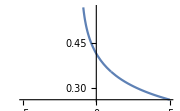

```mathematica
Plot[fp1183c[x],{x,-5,5},ImageSize->Small]
```

```mathematica
fp1183c[1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

É uma função da forma x^(1/2)/x^1, ou x^(-1/2).

```mathematica
Manipulate[Plot[x^n,{x,-10,10},ImageSize->Small],{{n,-.5},-2,2,.5}]
```

Ou seja, o grau resultante é -1/2, mas ela não é um polinômio deste grau. Ela é uma função racional e qual o overlap das funções racionais com as polinomiais? Pois as racionais têm grau, fracional (pode ser inteiro também?).

É a fatoração conjugado da raiz que fatora este racional.

Computação do difference quotient.

```mathematica
fdq[f_,x0_,x1_]:=(f[x0+x1]-f[x0])/(x0+x1-x0)
```

```mathematica
f1[x_]:=x^2
```

((3+x_1)^2-(3)^2)/x_1

```mathematica
fdq[f1,3,x]
```

(-9+(3+x)^2)/x

```mathematica
fdq[f1,3,0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[fdq[f1,3,x],x->0]
```

6

```mathematica
fdq[f1,3,1]
```

7

```mathematica
Limit[fdq[f1,3,x],x->1]
```

7

f_1(x) = If(3 < x < 5, (0.2x - 1).b3 + 5, (0.2x - 1).b3 + 3)

```mathematica
Clear[f2]
```

```mathematica
f2[x_]:=Piecewise[{{(0.2x-1)^3+5,3<x<5}},(0.2x-1)^3+3]
```

```mathematica
?f2
```

Global`f2

f2[x_]:=Piecewise[{{(0.2 x-1)^3+5,3<x<5}},(0.2 x-1)^3+3]

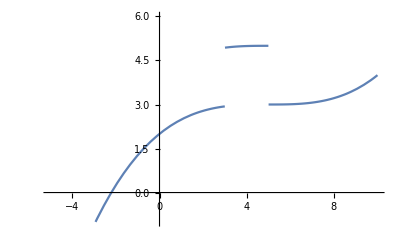

```mathematica
Plot[f2[x],{x,-5,10},PlotRange->{{-5,10},{-1,6}}]
```

```mathematica
{f2[2],f2[3],f2[4],f2[5],f2[6]}
```

{2.784,2.936,4.992,3.,3.008}

```mathematica
ratio[f_,x_]:=f[x]/x
```

```mathematica
?ratio
```

Global`ratio

ratio[f_,x_]:=f[x]/x

```mathematica
ratio[f2[x],x]
```

((Piecewise[{{5+(-1+0.2 x)^3, 3<x<5}, {3+(-1+0.2 x)^3, True}}])[x])/x

```mathematica
{ratio[f2,2],ratio[f2,3],ratio[f2,4],ratio[f2,5],ratio[f2,6]}
```

{1.392,0.978667,1.248,0.6,0.501333}

```mathematica
fdq[f2,2,x1]
```

(-2.784+(Piecewise[{{5+(-1+0.2 (2+x1))^3, 3<2+x1<5}, {3+(-1+0.2 (2+x1))^3, True}}]))/x1

A derivada é conforme x_1 (e não x_0) tende a zero.
Os seguintes limites são limites da função difference quotient da função original.

```mathematica
fdq[f2,2.9,1]
```

2.06344

y em x_1=0 não existe...

```mathematica
fdq[f2,2.9,0]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

O limite onde x_1≠0 é igual a y...

```mathematica
Limit[fdq[f2,2.9,x1],x1->1]
```

2.06344

O limite em x_1=0 existe.

```mathematica
Limit[fdq[f2,2.9,x1],x1->0]
```

0.10584

(Este é o slope da derivada em x_0=2.9.)
A derivada existe pois existe um limite completo em x_0=2.9.
Em x_0=3, não existe limite completo (só existe limite à esquerda).

```mathematica
f2[3]
```

2.936

```mathematica
fdq[f2,3,0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[fdq[f2,3,x1],x1->0]
```

Indeterminate

Em x_0>3, ele já existe...

```mathematica
Limit[fdq[f2,3.1,x1],x1->0]
```

0.08664

Mesmo em x_0=5.

```mathematica
Limit[fdq[f2,5,x1],x1->0]
```

Indeterminate

```mathematica
Limit[fdq[f2,4.9,x1],x1->0]
```

0.00024

Estes limites não existem, mantendo o denominador zero.
Não temos os valores dos limites mesmo existindo y:

```mathematica
Limit[f2[x],x->3]
```

Indeterminate

```mathematica
Limit[f2[x],x->2.9]
```

2.92591

```mathematica
Limit[f2[x],x->5]
```

Indeterminate

```mathematica
Limit[f2[x],x->5.1]
```

3.00001

Testar a criação de descontinuidade, limite e derivada sem ponto, mas primeiro com ponto (deslocado).

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
fdesl[x_]:=If[x≠2,(x-3)^2,3]
```

```mathematica
{fdesl[1.9],fdesl[2],fdesl[2.1]}
```

{1.21,3,0.81}

```mathematica
{Limit[fdesl[x],x->1.9],Limit[fdesl[x],x->2],Limit[fdesl[x],x->2.1]}
```

{1.21,1,0.81}

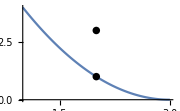

```mathematica
Plot[fdesl[x],{x,1,3},Epilog->{PointSize[.03],Point[{{2,fdesl[2]},{2,Limit[fdesl[x],x->2]}}]},ImageSize->Small]
```

```mathematica
?fdq
```

Global`fdq

fdq[f_,x0_,x1_]:=(f[x0+x1]-f[x0])/(x0+x1-x0)

```mathematica
Simplify[fdq[fdesl,2,x1]]
```

Piecewise[{{-2-2/x1+x1, x1≠0}, {0, True}}]

```mathematica
Limit[fdq[fdesl,1.5,x],x->0]
```

-3.

```mathematica
{fdesl'[0.5],fdesl'[1],fdesl'[1.5],fdesl'[1.9] ,fdesl'[2],fdesl'[2.1],fdesl'[2.5],fdesl'[3],fdesl'[3.5] }
```

{-5.,-4,-3.,-2.2,0,-1.8,-1.,0,1.}

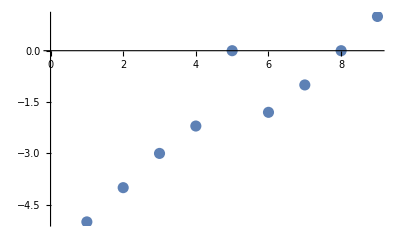

```mathematica
ListPlot[{fdesl'[0.5],fdesl'[1],fdesl'[1.5],fdesl'[1.9] ,fdesl'[2],fdesl'[2.1],fdesl'[2.5],fdesl'[3],fdesl'[3.5] },PlotStyle->PointSize[0.02]]
```

Ou seja, a derivada 0 em 2 está “diferente”.

```mathematica
fdesl'[x]
```

If[x≠2,2 (x-3),0]

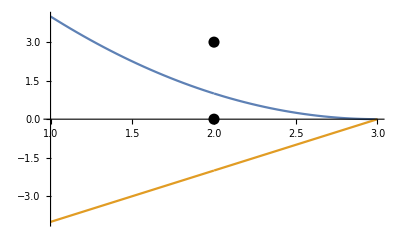

```mathematica
Plot[{fdesl[x],fdesl'[x]},{x,1,3},Epilog->{PointSize[0.02],Point[{{2,fdesl[2]},{2,fdesl'[2]}}]}]
```

Todas as “derivadas em pontos não-contínuos” são zero ou essa derivada realmente é zero?
Não importa, vamos tentar tomar a derivada no limite.

```mathematica
Limit[fdq[fdesl,2.1,x1],x1->0]
```

-1.8

```mathematica
Limit[fdesl[x],x->2]
```

1

```mathematica
fdq[fdesl,2,x1]
```

(-3+If[2+x1≠2,((2+x1)-3)^2,3])/x1

```mathematica
?fdq
```

Global`fdq

fdq[f_,x0_,x1_]:=(f[x0+x1]-f[x0])/(x0+x1-x0)

```mathematica
fdq[fdesl,Limit[fdesl[x0],x0->2],x1]
```

(-4+If[1+x1≠2,((1+x1)-3)^2,3])/x1

```mathematica
Limit[fdq[fdesl,Limit[fdesl[x0],x0->2],x1],x1->0]
```

-4

Isso deveria ser igual à derivada da função sem a descontinuidade.

```mathematica
?fdesl
```

Global`fdesl

fdesl[x_]:=If[x≠2,(x-3)^2,3]

```mathematica
fdeslfix[x_]:=(x-3)^2
```

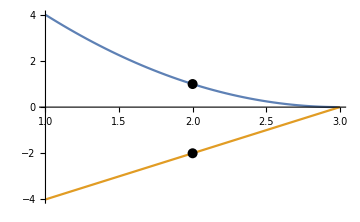

```mathematica
Plot[{fdeslfix[x],fdeslfix'[x]},{x,1,3},Epilog->{PointSize[0.02],Point[{{2,fdeslfix[2]},{2,fdeslfix'[2]}}]},ImageSize->Medium]
```

```mathematica
fdeslfix'[2]
```

-2

```mathematica
Limit[fdq[fdeslfix,2,x1],x1->0]
```

-2

Provavelmente o fdq em fdesl está lendo um y_0=3 ao invés de y_0=lim_(x_0→0) 2.
Precisaríamos reconstruir o fdq.

Eu consigo tomar qualquer limite em um ponto? (Sim, eu já havia tomado este limite acima.)

lim_(Δx→0) (f(x+Δx)-f(x))/Δx⇒lim_(Δx→0) (f(x+Δx)-lim_(x_1→0) f(x+x_1))/Δx.

Este é o fdql... (Nota: aparentemente eu estava usando x_1 erroneamente como Δx, quando x_1=x+Δx).

Primeiro só a parte do limite sobre uma função.

```mathematica
Clear[funclim]
funclim[f_,x_]:=Limit[f[xa],xa->x]
```

```mathematica
?funclim
```

Global`funclim

funclim[f_,x_]:=lim_(xa→x) f[xa]

```mathematica
funclim[fdesl,2]
```

1

```mathematica
Clear[fdqlim]
fdqlim[f_,x0_]:=(f[x0+Δx]-Limit[f[xa],xa->x0])/Δx
```

```mathematica
?fdqlim
```

Global`fdqlim

fdqlim[f_,x0_]:=(f[x0+Δx]-lim_(xa→x0) f[xa])/Δx

Este seria o limite final (genérico):

```mathematica
Limit[fdqlim[f,x0],Δx->0]
```

lim_(Δx→0) (f[x0+Δx]-lim_(xa→x0) f[xa])/Δx

Para f:

```mathematica
Limit[fdqlim[fdesl,x0],Δx->0]
```

Piecewise[{{2 (-3+x0), x0∈ℝ&&x0≠2}, {Indeterminate, True}}]

Para f e 2 sem limite:

```mathematica
fdqlim[fdesl,2]
```

(-1+If[2+Δx≠2,((2+Δx)-3)^2,3])/Δx

Para f e 2 com limite:

```mathematica
Limit[fdqlim[fdesl,2],Δx->0]
```

-2

Funcionou.

```mathematica
dlim[f_,x0_]:=Limit[fdqlim[f,x0],Δx->0]
```

```mathematica
?dlim
```

Global`dlim

dlim[f_,x0_]:=lim_(Δx→0) fdqlim[f,x0]

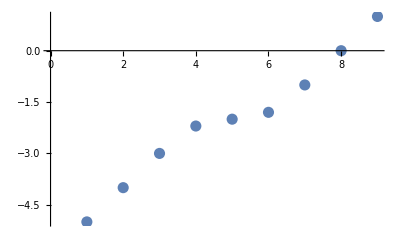

```mathematica
ListPlot[{dlim[fdesl,0.5],dlim[fdesl,1],dlim[fdesl,1.5],dlim[fdesl,1.9],dlim[fdesl,2],dlim[fdesl,2.1],dlim[fdesl,2.5],dlim[fdesl,3],dlim[fdesl,3.5] },PlotStyle->PointSize[0.02]]
```

O que é essa p*? dq seria (f(x+Δx)-f(x))/Δx=((x+Δx)^2+2-(x^2+2))/Δx=(x^2+2xΔx+Δx^2+2-x^2-2)/Δx=(Δx(2x+Δx))/Δx=2x+Δx, que tende a 2x conforme Δx tende a zero.

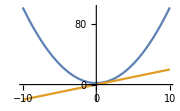

```mathematica
Plot[{f,2x},{x,-10,10},ImageSize->Small]
```

Na verdade, preciso tender isso a zero, não a 3. E também... o limite constante é ponto, não reta.

(Observando que a razão —difference quotient [Silverman]—implica uma aritmética, mas neste caso, de execuções de funções.)

A aritmética da função difference quotient explica a redução de grau da derivada. A difference quotient é uma função que “tira um grau” de uma função. É uma função composta? Com como parâmetro uma função? Necessariamente com denominador de um grau a menos que o numerador. Portanto um tipo de objeto específico.

## p. 118

lim_(x→5) (√(2x-1)-3)/(x-5).

```mathematica
Clear[f1183e]
f1183e[x_]:=(√(2x-1)-3)/(x-5)
```

```mathematica
?f1183e
```

Global`f1183e

f1183e[x_]:=(√(2 x-1)-3)/(x-5)

```mathematica
Numerator[f1183e[x]]
```

-3+√(-1+2 x)

```mathematica
Clear[f1183eb]
```

```mathematica
f1183eb[x_]=Simplify[Numerator[f1183e[x]]*(√(2x-1)+3)]/Simplify[Denominator[f1183e[x]]*(√(2x-1)+3)]
```

2/(3+√(-1+2 x))

```mathematica
f1183eb[x]
```

2/(3+√(-1+2 x))

```mathematica
f1183eb[5]
```

1/3

```mathematica
Limit[f1183e[x],x->5]
```

1/3

```mathematica
Expand[(x+1)^4]
```

1+4 x+6 x^2+4 x^3+x^4